lim_(e→0) {(Cos[2 π fnfact[7 n]] Sin[2 π fnfact[n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[n]] Sin[2 π fnfact[7 n]] Sin[2 π fnfact[e+n]]+Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[7 n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[7 n]] Sin[2 π fnfact[n]] Sin[2 π fnfact[7 (e+n)]]+Cos[2 π fnfact[e+n]] Sin[2 π fnfact[n]] Sin[2 π fnfact[7 (e+n)]]+Cos[2 π fnfact[n]] Sin[2 π fnfact[7 n]] Sin[2 π fnfact[7 (e+n)]]-Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 n]] Sin[2 π fnfact[7 (e+n)]])/(-Cos[2 π fnfact[e+n]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 n]]-Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[7 n]]+Cos[2 π fnfact[n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[7 n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[n]] Sin[2 π fnfact[7 (e+n)]]+Cos[2 π fnfact[7 n]] Sin[2 π fnfact[7 (e+n)]]),(-Cos[2 π fnfact[7 n]] Cos[2 π fnfact[e+n]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[7 n]] Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[n]] Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 n]]-Cos[2 π fnfact[n]] Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[7 n]]+Cos[2 π fnfact[n]] Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[7 n]] Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[n]] Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 (e+n)]]+Cos[2 π fnfact[7 n]] Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 (e+n)]])/(-Cos[2 π fnfact[e+n]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[n]]+Cos[2 π fnfact[e+n]] Sin[2 π fnfact[7 n]]-Cos[2 π fnfact[7 (e+n)]] Sin[2 π fnfact[7 n]]+Cos[2 π fnfact[n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[7 n]] Sin[2 π fnfact[e+n]]-Cos[2 π fnfact[n]] Sin[2 π fnfact[7 (e+n)]]+Cos[2 π fnfact[7 n]] Sin[2 π fnfact[7 (e+n)]])}

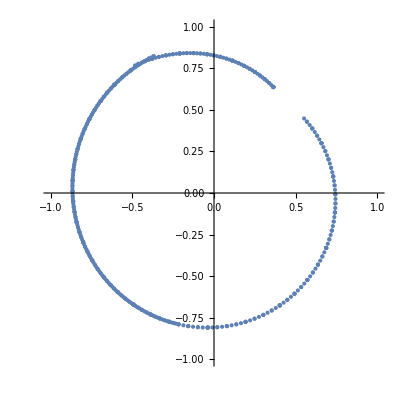

```mathematica
Remove[rotate,intersect,rotate2,intersect2,start,stop,step,e,fnline,fnfact,pdata];

rotate[n_]:=(alpha=2*Pi*fnfact[n];x=-Sin[alpha];y=Cos[alpha];{x,y});
intersect[n_,e_]:=(line1={rotate[n],rotate[fnline[n]]};line2={rotate[n+e],rotate[fnline[n+e]]};a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];{detx/det,dety/det});

rotate2[n_]:=(alpha=2*Pi*(n/(2^(IntegerPart[Log[2,n]]+1)-2^IntegerPart[Log[2,n]]));x=-Sin[alpha];y=Cos[alpha];{x,y});
intersect2[n_,e_]:=(line1={rotate2[n],rotate2[n*7]};line2={rotate2[n+e],rotate2[(n+e)*7]};a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];{detx/det,dety/det});

(* l=Limit[intersect[n,d,e],{d,e}->{Infinity,0}]; *)

l=Limit[intersect2[n,e],e->0];
Print[l];

start=1;
stop=100;
step=0.2;

e=0.001;
fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(IntegerPart[Log[2,n]]+1)-2^IntegerPart[Log[2,n]]);
pdata=Table[intersect[n,e],{n,start,stop,step}];
ListPlot[{pdata},PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```